```mathematica
β[ω_,δ_,t_,ϵ_]:=β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[10],Join[Table[{i,i-1},{i,Range[2,10,1]}],Table[{i,i+1},{i,Range[1,10,1]}]]->-t]
```

```mathematica
T[t_]:=T[t]=t*IdentityMatrix[10]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,δ,1,0]],A:=Inverse[β[ω,δ,1,0]],T:=T[1]},Do[J=Inverse[IdentityMatrix[10]-A.T.J.T].A,13200];J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[10]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[10]-g[ω,δ,t,ϵ].T[1].LEFT[ω,δ,t,ϵ].T[1]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[10]-SL[ω,δ,1,0].T[1].SR[ω,δ,1,0].T[1]].SL[ω,δ,1,0]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[10]-SR[ω,δ,1,0].T[1].SL[ω,δ,1,0].T[1]].SR[ω,δ,1,0]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,1,0].T[1].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Tr[gdd[ω,δ,t,ϵ].T[1].grr[ω,δ,t,ϵ].T[1]-T[1].GNON[ω,δ,t,ϵ].T[1].GNON[ω,δ,t,ϵ]]
```

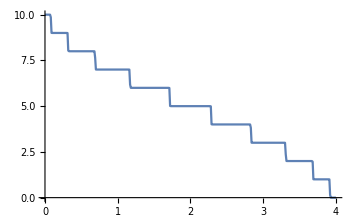
{307.204,-Graphics-}

```mathematica
Timing[ListLinePlot[Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[0,4,0.01]}]]]
```

```mathematica
pris:=pris=Table[{ω,Abs[tr[ω,0.001,1,0]]},{ω,Range[0,4,0.01]}]
```

```mathematica
pris
```

{{0.,9.99991},{0.01,9.99991},{0.02,9.9999},{0.03,9.99987},{0.04,9.99982},{0.05,9.99971},{0.06,9.99941},{0.07,9.99792},{0.08,9.8559},{0.09,9.00303},{0.1,9.00067},{0.11,9.00027},{0.12,9.00014},{0.13,9.00008},{0.14,9.00005},{0.15,9.00003},{0.16,9.00002},{0.17,9.00001},{0.18,9.},{0.19,9.},{0.2,8.99999},{0.21,8.99998},{0.22,8.99998},{0.23,8.99997},{0.24,8.99996},{0.25,8.99994},{0.26,8.99992},{0.27,8.99989},{0.28,8.99982},{0.29,8.99966},{0.3,8.99918},{0.31,8.99559},{0.32,8.03553},{0.33,8.00158},{0.34,8.00048},{0.35,8.00023},{0.36,8.00013},{0.37,8.00008},{0.38,8.00006},{0.39,8.00004},{0.4,8.00003},{0.41,8.00002},{0.42,8.00002},{0.43,8.00001},{0.44,8.00001},{0.45,8.00001},{0.46,8.},{0.47,8.},{0.48,8.},{0.49,8.},{0.5,8.},{0.51,8.},{0.52,7.99999},{0.53,7.99999},{0.54,7.99999},{0.55,7.99999},{0.56,7.99999},{0.57,7.99998},{0.58,7.99998},{0.59,7.99997},{0.6,7.99997},{0.61,7.99996},{0.62,7.99995},{0.63,7.99993},{0.64,7.9999},{0.65,7.99984},{0.66,7.99972},{0.67,7.99939},{0.68,7.99764},{0.69,7.63404},{0.7,7.00261},{0.71,7.00063},{0.72,7.00028},{0.73,7.00015},{0.74,7.0001},{0.75,7.00007},{0.76,7.00005},{0.77,7.00003},{0.78,7.00003},{0.79,7.00002},{0.8,7.00002},{0.81,7.00001},{0.82,7.00001},{0.83,7.00001},{0.84,7.00001},{0.85,7.},{0.86,7.},{0.87,7.},{0.88,7.},{0.89,7.},{0.9,7.},{0.91,7.},{0.92,7.},{0.93,7.},{0.94,7.},{0.95,7.},{0.96,7.},{0.97,6.99999},{0.98,6.99999},{0.99,6.99999},{1.,6.99999},{1.01,6.99999},{1.02,6.99999},{1.03,6.99999},{1.04,6.99998},{1.05,6.99998},{1.06,6.99998},{1.07,6.99997},{1.08,6.99997},{1.09,6.99996},{1.1,6.99995},{1.11,6.99993},{1.12,6.99989},{1.13,6.99983},{1.14,6.9997},{1.15,6.99931},{1.16,6.99704},{1.17,6.18056},{1.18,6.0021},{1.19,6.00057},{1.2,6.00026},{1.21,6.00015},{1.22,6.00009},{1.23,6.00006},{1.24,6.00005},{1.25,6.00003},{1.26,6.00003},{1.27,6.00002},{1.28,6.00002},{1.29,6.00001},{1.3,6.00001},{1.31,6.00001},{1.32,6.00001},{1.33,6.00001},{1.34,6.},{1.35,6.},{1.36,6.},{1.37,6.},{1.38,6.},{1.39,6.},{1.4,6.},{1.41,6.},{1.42,6.},{1.43,6.},{1.44,6.},{1.45,6.},{1.46,6.},{1.47,6.},{1.48,6.},{1.49,6.},{1.5,5.99999},{1.51,5.99999},{1.52,5.99999},{1.53,5.99999},{1.54,5.99999},{1.55,5.99999},{1.56,5.99999},{1.57,5.99999},{1.58,5.99999},{1.59,5.99998},{1.6,5.99998},{1.61,5.99998},{1.62,5.99997},{1.63,5.99996},{1.64,5.99995},{1.65,5.99994},{1.66,5.99992},{1.67,5.99987},{1.68,5.9998},{1.69,5.99961},{1.7,5.99894},{1.71,5.99153},{1.72,5.01124},{1.73,5.00115},{1.74,5.00041},{1.75,5.0002},{1.76,5.00012},{1.77,5.00008},{1.78,5.00006},{1.79,5.00004},{1.8,5.00003},{1.81,5.00002},{1.82,5.00002},{1.83,5.00002},{1.84,5.00001},{1.85,5.00001},{1.86,5.00001},{1.87,5.00001},{1.88,5.00001},{1.89,5.},{1.9,5.},{1.91,5.},{1.92,5.},{1.93,5.},{1.94,5.},{1.95,5.},{1.96,5.},{1.97,5.},{1.98,5.},{1.99,5.},{2.,5.},{2.01,5.},{2.02,5.},{2.03,5.},{2.04,5.},{2.05,5.},{2.06,5.},{2.07,4.99999},{2.08,4.99999},{2.09,4.99999},{2.1,4.99999},{2.11,4.99999},{2.12,4.99999},{2.13,4.99999},{2.14,4.99999},{2.15,4.99998},{2.16,4.99998},{2.17,4.99998},{2.18,4.99998},{2.19,4.99997},{2.2,4.99996},{2.21,4.99995},{2.22,4.99994},{2.23,4.99991},{2.24,4.99987},{2.25,4.99979},{2.26,4.99958},{2.27,4.99883},{2.28,4.9887},{2.29,4.00843},{2.3,4.00105},{2.31,4.00038},{2.32,4.00019},{2.33,4.00012},{2.34,4.00008},{2.35,4.00005},{2.36,4.00004},{2.37,4.00003},{2.38,4.00002},{2.39,4.00002},{2.4,4.00002},{2.41,4.00001},{2.42,4.00001},{2.43,4.00001},{2.44,4.00001},{2.45,4.00001},{2.46,4.},{2.47,4.},{2.48,4.},{2.49,4.},{2.5,4.},{2.51,4.},{2.52,4.},{2.53,4.},{2.54,4.},{2.55,4.},{2.56,4.},{2.57,4.},{2.58,4.},{2.59,4.},{2.6,4.},{2.61,4.},{2.62,3.99999},{2.63,3.99999},{2.64,3.99999},{2.65,3.99999},{2.66,3.99999},{2.67,3.99999},{2.68,3.99999},{2.69,3.99999},{2.7,3.99998},{2.71,3.99998},{2.72,3.99998},{2.73,3.99997},{2.74,3.99997},{2.75,3.99996},{2.76,3.99995},{2.77,3.99993},{2.78,3.9999},{2.79,3.99985},{2.8,3.99973},{2.81,3.99942},{2.82,3.99787},{2.83,3.81924},{2.84,3.00293},{2.85,3.00067},{2.86,3.00029},{2.87,3.00016},{2.88,3.0001},{2.89,3.00007},{2.9,3.00005},{2.91,3.00004},{2.92,3.00003},{2.93,3.00002},{2.94,3.00002},{2.95,3.00001},{2.96,3.00001},{2.97,3.00001},{2.98,3.00001},{2.99,3.00001},{3.,3.},{3.01,3.},{3.02,3.},{3.03,3.},{3.04,3.},{3.05,3.},{3.06,3.},{3.07,3.},{3.08,3.},{3.09,3.},{3.1,3.},{3.11,2.99999},{3.12,2.99999},{3.13,2.99999},{3.14,2.99999},{3.15,2.99999},{3.16,2.99999},{3.17,2.99999},{3.18,2.99998},{3.19,2.99998},{3.2,2.99998},{3.21,2.99997},{3.22,2.99997},{3.23,2.99996},{3.24,2.99995},{3.25,2.99993},{3.26,2.9999},{3.27,2.99984},{3.28,2.99971},{3.29,2.99935},{3.3,2.99736},{3.31,2.36572},{3.32,2.00234},{3.33,2.0006},{3.34,2.00027},{3.35,2.00015},{3.36,2.00009},{3.37,2.00006},{3.38,2.00005},{3.39,2.00003},{3.4,2.00003},{3.41,2.00002},{3.42,2.00001},{3.43,2.00001},{3.44,2.00001},{3.45,2.00001},{3.46,2.},{3.47,2.},{3.48,2.},{3.49,2.},{3.5,2.},{3.51,2.},{3.52,1.99999},{3.53,1.99999},{3.54,1.99999},{3.55,1.99999},{3.56,1.99998},{3.57,1.99998},{3.58,1.99998},{3.59,1.99997},{3.6,1.99996},{3.61,1.99995},{3.62,1.99993},{3.63,1.99991},{3.64,1.99986},{3.65,1.99976},{3.66,1.9995},{3.67,1.9984},{3.68,1.96437},{3.69,1.00437},{3.7,1.0008},{3.71,1.00032},{3.72,1.00017},{3.73,1.0001},{3.74,1.00007},{3.75,1.00004},{3.76,1.00003},{3.77,1.00002},{3.78,1.00001},{3.79,1.00001},{3.8,0.999999},{3.81,0.999993},{3.82,0.999987},{3.83,0.999979},{3.84,0.999969},{3.85,0.999955},{3.86,0.999934},{3.87,0.999901},{3.88,0.999839},{3.89,0.999704},{3.9,0.999307},{3.91,0.996924},{3.92,0.143905},{3.93,0.00204127},{3.94,0.000563298},{3.95,0.000259464},{3.96,0.00014904},{3.97,0.0000968954},{3.98,0.0000681989},{3.99,0.0000507273},{4.,0.0000392968}}

```mathematica
imp[ω_,δ_,t_,ϵ_,ϵ1_]:=Inverse[Module[{gg=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,10}]},ReplacePart[gg,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]]
```

```mathematica
tr1[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[10],imp=Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,10}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]](*,m=RandomInteger[{0,1}],n=RandomInteger[{0,1}],o=RandomInteger[{0,1}],p=RandomInteger[{0,1}],q=RandomInteger[{0,1}]*)},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,RandomInteger[{0,1}]]; J=J];sl2=Inverse[IdentityMatrix[10]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,RandomInteger[{0,1}]]; J=J];sl4=Inverse[IdentityMatrix[10]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,RandomInteger[{0,1}]]; J=J];sl6=Inverse[IdentityMatrix[10]-imp.T.sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,RandomInteger[{0,1}]]; J=J];sl8=Inverse[IdentityMatrix[10]-imp.T.sl7.T].imp; sl9=Module[{J=sl8},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,RandomInteger[{0,1}]]; J=J];sl10=Inverse[IdentityMatrix[10]-imp.T.sl9.T].imp; sl11=Module[{J=sl10},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,RandomInteger[{0,1}]]; J=J];sl12=Inverse[IdentityMatrix[10]-imp.T.sl11.T].imp; sl13=Module[{J=sl12},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,RandomInteger[{0,1}]]; J=J];sl14=Inverse[IdentityMatrix[10]-imp.T.sl13.T].imp; sl15=Module[{J=sl14},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,RandomInteger[{0,1}]]; J=J];sl16=Inverse[IdentityMatrix[10]-imp.T.sl15.T].imp; sl17=Module[{J=sl16},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,RandomInteger[{0,1}]]; J=J];Il1:=Inverse[IdentityMatrix[10]-sl17.T.SR[ω,δ,1,0].T].sl17;
Ir1:=Inverse[IdentityMatrix[10]-SR[ω,δ,1,0].T.sl17.T].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].T.Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]
```

```mathematica
tr1[0.1,0.001,1,0,1]
```

6.49249

```mathematica
ListLinePlot[Table[{ω,Mean[Table[tr1[ω,0.001,1,0,0.7],1000]]},{ω,Range[0,4,0.01]}]]
```

$Aborted

```mathematica
Export["10sq8imp7.csv",Table[{ω,Mean[Table[tr1[ω,0.001,1,0,0.7],1000]]},{ω,Range[0,4,0.01]}]]
```

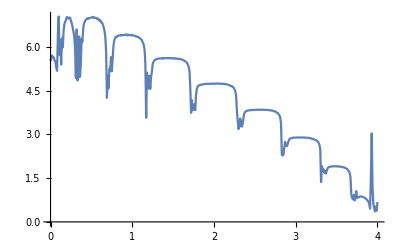

```mathematica
ListLinePlot[Import["10sq6imp7.csv"]]
```

```mathematica
Export["10sq8imp3.csv",Table[{ω,Mean[Table[tr1[ω,0.001,1,0,0.3],1000]]},{ω,Range[0,4,0.01]}]]
```

10sq6imp4.csv

```mathematica
Export["10sq8imp5.csv",Table[{ω,Mean[Table[tr1[ω,0.001,1,0,0.5],1000]]},{ω,Range[0,4,0.01]}]]
```

10sq6imp8.csv

```mathematica
Export["10sq6imp9.csv",f[0.9]]
```

10sq6imp9.csv

```mathematica
Export["10sq6imp1.csv",f[1]]
```

10sq6imp1.csv

```mathematica
Export["10sq6imp12.csv",f[1.2]]
```

10sq6imp12.csv

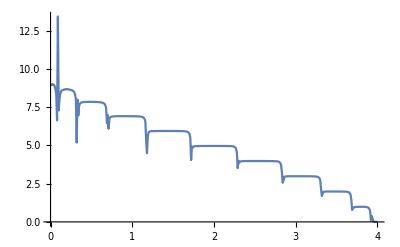

```mathematica
ListLinePlot[f[0.3]]
```

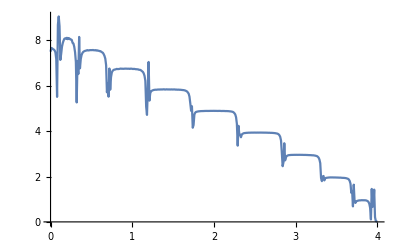

```mathematica
ListLinePlot[f[0.5]]
```

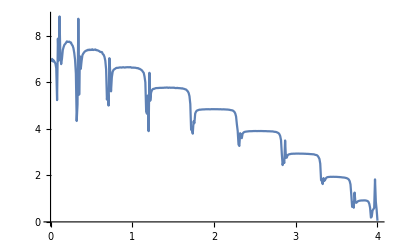

```mathematica
ListLinePlot[f[0.6]]
```

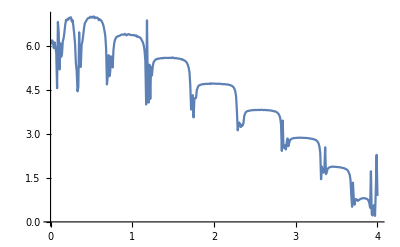

```mathematica
ListLinePlot[f[0.8]]
```

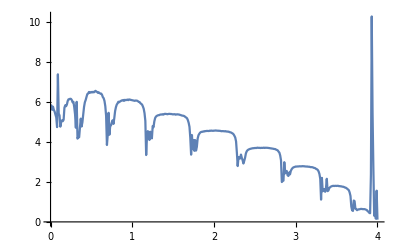

```mathematica
ListLinePlot[f[1.0]]
```

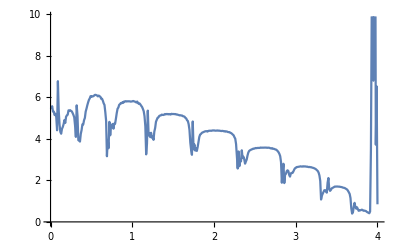

```mathematica
ListLinePlot[f[1.2]]
```

```mathematica
tr5[ω_,δ_,t_,ϵ_,ϵ1_]:=Module[{gg=g[ω,δ,t,ϵ],T=t*IdentityMatrix[10],imp=Inverse[Module[{κ=β[ω,δ,t,ϵ],μ1=RandomInteger[{1,10}]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*δ-ϵ1]]],m=RandomInteger[{0,1}],n=RandomInteger[{0,1}],o=RandomInteger[{0,1}],p=RandomInteger[{0,1}],q=RandomInteger[{0,1}],r=RandomInteger[{0,1}]},sl1= Module[{J=SL[ω,δ,t,ϵ]},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,m]; J=J];sl2=Inverse[IdentityMatrix[10]-imp.T.sl1.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,n]; J=J];sl4=Inverse[IdentityMatrix[10]-imp.T.sl3.T].imp; sl5=Module[{J=sl4},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,o]; J=J];sl6=Inverse[IdentityMatrix[10]-imp.T.sl5.T].imp; sl7=Module[{J=sl6},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,p]; J=J];sl8=Inverse[IdentityMatrix[10]-imp.T.sl7.T].imp; sl9=Module[{J=sl8},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,q]; J=J];sl10=Inverse[IdentityMatrix[10]-imp.T.sl9.T].imp; sl11=Module[{J=sl10},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,m]; J=J];sl12=Inverse[IdentityMatrix[10]-imp.T.sl11.T].imp; sl13=Module[{J=sl12},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,m]; J=J];sl14=Inverse[IdentityMatrix[10]-imp.T.sl13.T].imp; sl15=Module[{J=sl14},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,o]; J=J];Il1:=Inverse[IdentityMatrix[10]-sl11.T.SR[ω,δ,1,0].T].sl11;
Ir1:=Inverse[IdentityMatrix[10]-SR[ω,δ,1,0].T.sl11.T].SR[ω,δ,1,0];
gdd1:= Il1-ConjugateTranspose[Il1];
grr1:= Ir1-ConjugateTranspose[Ir1];
Gnonlocal1:= SR[ω,δ,1,0].T.Il1;
GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];
{{Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]],m+n+o+p+q+8}}]
```

```mathematica
N[Max[Table[tr5[1,0.001,1,0,1][[1,2]],10000]]]
```

13.

```mathematica
s[ϵ1_]:=s[ϵ1]=Table[{ω,Mean[Table[tr5[ω,0.001,1,0,ϵ1][[1,1]],1000]]},{ω,Range[0,4,0.01]}]
```

```mathematica
s[0.7]
```

{{0.,6.76183},{0.01,6.65716},{0.02,6.76552},{0.03,6.75051},{0.04,6.78991},{0.05,6.5691},{0.06,6.46446},{0.07,6.18029},{0.08,4.19643},{0.09,6.7416},{0.1,7.25331},{0.11,8.12698},{0.12,6.74799},{0.13,6.57942},{0.14,6.47692},{0.15,6.83687},{0.16,7.18392},{0.17,7.34862},{0.18,7.39832},{0.19,7.50078},{0.2,7.5275},{0.21,7.54431},{0.22,7.54155},{0.23,7.58675},{0.24,7.58098},{0.25,7.53846},{0.26,7.46196},{0.27,7.4556},{0.28,7.30718},{0.29,7.11439},{0.3,6.77158},{0.31,6.47764},{0.32,4.48583},{0.33,4.82671},{0.34,8.91925},{0.35,4.88115},{0.36,6.57174},{0.37,6.07476},{0.38,6.43344},{0.39,6.83315},{0.4,7.03511},{0.41,7.1167},{0.42,7.17429},{0.43,7.21657},{0.44,7.24065},{0.45,7.25839},{0.46,7.27379},{0.47,7.26614},{0.48,7.25893},{0.49,7.28459},{0.5,7.29919},{0.51,7.29068},{0.52,7.28447},{0.53,7.31048},{0.54,7.29943},{0.55,7.29647},{0.56,7.28274},{0.57,7.29027},{0.58,7.27385},{0.59,7.26609},{0.6,7.25507},{0.61,7.23209},{0.62,7.18363},{0.63,7.15495},{0.64,7.11579},{0.65,7.03851},{0.66,6.95178},{0.67,6.77892},{0.68,6.5025},{0.69,5.11391},{0.7,7.13323},{0.71,4.50834},{0.72,6.28726},{0.73,5.69267},{0.74,5.75639},{0.75,5.89924},{0.76,6.24497},{0.77,6.38168},{0.78,6.44802},{0.79,6.49308},{0.8,6.50753},{0.81,6.53009},{0.82,6.55366},{0.83,6.56171},{0.84,6.56814},{0.85,6.56115},{0.86,6.58382},{0.87,6.56887},{0.88,6.59034},{0.89,6.58958},{0.9,6.58386},{0.91,6.58567},{0.92,6.58295},{0.93,6.59944},{0.94,6.58574},{0.95,6.57645},{0.96,6.59953},{0.97,6.58711},{0.98,6.58779},{0.99,6.57438},{1.,6.57218},{1.01,6.57395},{1.02,6.57883},{1.03,6.57208},{1.04,6.55922},{1.05,6.55385},{1.06,6.55224},{1.07,6.53825},{1.08,6.52167},{1.09,6.50841},{1.1,6.49207},{1.11,6.45693},{1.12,6.41877},{1.13,6.36127},{1.14,6.28742},{1.15,6.1353},{1.16,5.8991},{1.17,4.53447},{1.18,4.5219},{1.19,4.49736},{1.2,4.31498},{1.21,6.06332},{1.22,4.93453},{1.23,5.32285},{1.24,5.51328},{1.25,5.61323},{1.26,5.64526},{1.27,5.66761},{1.28,5.67656},{1.29,5.69217},{1.3,5.69709},{1.31,5.7032},{1.32,5.71009},{1.33,5.71448},{1.34,5.7166},{1.35,5.71732},{1.36,5.72309},{1.37,5.72409},{1.38,5.72395},{1.39,5.7307},{1.4,5.72802},{1.41,5.72126},{1.42,5.7275},{1.43,5.72543},{1.44,5.72624},{1.45,5.72791},{1.46,5.72254},{1.47,5.73145},{1.48,5.73009},{1.49,5.72766},{1.5,5.71841},{1.51,5.72656},{1.52,5.72173},{1.53,5.71575},{1.54,5.72309},{1.55,5.71405},{1.56,5.7109},{1.57,5.70808},{1.58,5.70762},{1.59,5.70261},{1.6,5.69512},{1.61,5.6876},{1.62,5.6822},{1.63,5.67099},{1.64,5.6558},{1.65,5.63081},{1.66,5.61426},{1.67,5.5822},{1.68,5.51918},{1.69,5.4261},{1.7,5.28967},{1.71,4.95327},{1.72,3.85072},{1.73,3.83137},{1.74,3.4929},{1.75,3.9282},{1.76,3.93563},{1.77,4.4789},{1.78,4.6625},{1.79,4.70309},{1.8,4.73839},{1.81,4.76128},{1.82,4.7718},{1.83,4.77653},{1.84,4.78434},{1.85,4.78566},{1.86,4.79481},{1.87,4.79774},{1.88,4.79657},{1.89,4.8042},{1.9,4.80319},{1.91,4.80688},{1.92,4.80395},{1.93,4.80741},{1.94,4.80722},{1.95,4.80686},{1.96,4.80829},{1.97,4.80628},{1.98,4.80929},{1.99,4.80793},{2.,4.80823},{2.01,4.81375},{2.02,4.81133},{2.03,4.8151},{2.04,4.8118},{2.05,4.81027},{2.06,4.80785},{2.07,4.80888},{2.08,4.80925},{2.09,4.81026},{2.1,4.8036},{2.11,4.80734},{2.12,4.80307},{2.13,4.79999},{2.14,4.79513},{2.15,4.79334},{2.16,4.79838},{2.17,4.78891},{2.18,4.78511},{2.19,4.77699},{2.2,4.76423},{2.21,4.75632},{2.22,4.74144},{2.23,4.72251},{2.24,4.6884},{2.25,4.63035},{2.26,4.56068},{2.27,4.41406},{2.28,4.09725},{2.29,4.36943},{2.3,3.16913},{2.31,3.14765},{2.32,3.58831},{2.33,3.94123},{2.34,3.34579},{2.35,3.63981},{2.36,3.74973},{2.37,3.80265},{2.38,3.82562},{2.39,3.83778},{2.4,3.85009},{2.41,3.85662},{2.42,3.86156},{2.43,3.86656},{2.44,3.87134},{2.45,3.87194},{2.46,3.87239},{2.47,3.87323},{2.48,3.87612},{2.49,3.87892},{2.5,3.87974},{2.51,3.87864},{2.52,3.88058},{2.53,3.87884},{2.54,3.88258},{2.55,3.87945},{2.56,3.87884},{2.57,3.88085},{2.58,3.88153},{2.59,3.87972},{2.6,3.88024},{2.61,3.8803},{2.62,3.88041},{2.63,3.8796},{2.64,3.87585},{2.65,3.87548},{2.66,3.87141},{2.67,3.87268},{2.68,3.87173},{2.69,3.86783},{2.7,3.86644},{2.71,3.86136},{2.72,3.85701},{2.73,3.85362},{2.74,3.84632},{2.75,3.83755},{2.76,3.82113},{2.77,3.81343},{2.78,3.78794},{2.79,3.75152},{2.8,3.69319},{2.81,3.59396},{2.82,3.42623},{2.83,2.87409},{2.84,2.21524},{2.85,2.45172},{2.86,2.50183},{2.87,3.54044},{2.88,2.972},{2.89,2.57245},{2.9,2.77781},{2.91,2.83806},{2.92,2.86832},{2.93,2.88385},{2.94,2.89055},{2.95,2.89865},{2.96,2.90526},{2.97,2.90668},{2.98,2.91351},{2.99,2.91288},{3.,2.91224},{3.01,2.91538},{3.02,2.91381},{3.03,2.91272},{3.04,2.91093},{3.05,2.91362},{3.06,2.9118},{3.07,2.91324},{3.08,2.91381},{3.09,2.91177},{3.1,2.91068},{3.11,2.90999},{3.12,2.90416},{3.13,2.90847},{3.14,2.90668},{3.15,2.89867},{3.16,2.90079},{3.17,2.89471},{3.18,2.89299},{3.19,2.89147},{3.2,2.88698},{3.21,2.88409},{3.22,2.87035},{3.23,2.86266},{3.24,2.84847},{3.25,2.83209},{3.26,2.80464},{3.27,2.76443},{3.28,2.72007},{3.29,2.61507},{3.3,2.43733},{3.31,1.71117},{3.32,1.63971},{3.33,1.47073},{3.34,2.1838},{3.35,1.63653},{3.36,1.59645},{3.37,1.79214},{3.38,1.84151},{3.39,1.87543},{3.4,1.88834},{3.41,1.89676},{3.42,1.90472},{3.43,1.90686},{3.44,1.91121},{3.45,1.91373},{3.46,1.91288},{3.47,1.91046},{3.48,1.91293},{3.49,1.91471},{3.5,1.9107},{3.51,1.90912},{3.52,1.91101},{3.53,1.90364},{3.54,1.90614},{3.55,1.90208},{3.56,1.89727},{3.57,1.89536},{3.58,1.89059},{3.59,1.89081},{3.6,1.88271},{3.61,1.87462},{3.62,1.85802},{3.63,1.83917},{3.64,1.81598},{3.65,1.77666},{3.66,1.70401},{3.67,1.55069},{3.68,1.11787},{3.69,0.626707},{3.7,1.17741},{3.71,0.561737},{3.72,1.1272},{3.73,0.980606},{3.74,0.796034},{3.75,0.775168},{3.76,0.805733},{3.77,0.827248},{3.78,0.856707},{3.79,0.876079},{3.8,0.884774},{3.81,0.885107},{3.82,0.892258},{3.83,0.893698},{3.84,0.887177},{3.85,0.881624},{3.86,0.872685},{3.87,0.85906},{3.88,0.825727},{3.89,0.75941},{3.9,0.673383},{3.91,0.471337},{3.92,0.282469},{3.93,0.236259},{3.94,1.59656},{3.95,0.628264},{3.96,1.10185},{3.97,1.25479},{3.98,2.74268},{3.99,1.68145},{4.,0.702743}}

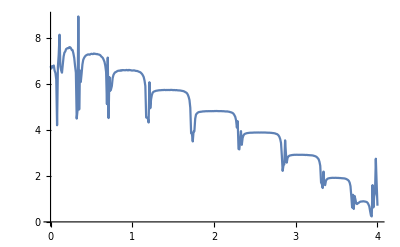

```mathematica
ListPlot[%63,Joined->True]
```

```mathematica
Export["sq5imp7.dat",s[0.7]]
```

sq5imp7.dat

```mathematica
Export["10sq5imp7.dat",s[0.7]]
```

10sq5imp7.dat

```mathematica
Import["10sq5imp7.dat"]
```

{{0.,6.76183},{0.01,6.65716},{0.02,6.76552},{0.03,6.75051},{0.04,6.78991},{0.05,6.5691},{0.06,6.46446},{0.07,6.18029},{0.08,4.19643},{0.09,6.7416},{0.1,7.25331},{0.11,8.12698},{0.12,6.74799},{0.13,6.57942},{0.14,6.47692},{0.15,6.83687},{0.16,7.18392},{0.17,7.34862},{0.18,7.39832},{0.19,7.50078},{0.2,7.5275},{0.21,7.54431},{0.22,7.54155},{0.23,7.58675},{0.24,7.58098},{0.25,7.53846},{0.26,7.46196},{0.27,7.4556},{0.28,7.30718},{0.29,7.11439},{0.3,6.77158},{0.31,6.47764},{0.32,4.48583},{0.33,4.82671},{0.34,8.91925},{0.35,4.88115},{0.36,6.57174},{0.37,6.07476},{0.38,6.43344},{0.39,6.83315},{0.4,7.03511},{0.41,7.1167},{0.42,7.17429},{0.43,7.21657},{0.44,7.24065},{0.45,7.25839},{0.46,7.27379},{0.47,7.26614},{0.48,7.25893},{0.49,7.28459},{0.5,7.29919},{0.51,7.29068},{0.52,7.28447},{0.53,7.31048},{0.54,7.29943},{0.55,7.29647},{0.56,7.28274},{0.57,7.29027},{0.58,7.27385},{0.59,7.26609},{0.6,7.25507},{0.61,7.23209},{0.62,7.18363},{0.63,7.15495},{0.64,7.11579},{0.65,7.03851},{0.66,6.95178},{0.67,6.77892},{0.68,6.5025},{0.69,5.11391},{0.7,7.13323},{0.71,4.50834},{0.72,6.28726},{0.73,5.69267},{0.74,5.75639},{0.75,5.89924},{0.76,6.24497},{0.77,6.38168},{0.78,6.44802},{0.79,6.49308},{0.8,6.50753},{0.81,6.53009},{0.82,6.55366},{0.83,6.56171},{0.84,6.56814},{0.85,6.56115},{0.86,6.58382},{0.87,6.56887},{0.88,6.59034},{0.89,6.58958},{0.9,6.58386},{0.91,6.58567},{0.92,6.58295},{0.93,6.59944},{0.94,6.58574},{0.95,6.57645},{0.96,6.59953},{0.97,6.58711},{0.98,6.58779},{0.99,6.57438},{1.,6.57218},{1.01,6.57395},{1.02,6.57883},{1.03,6.57208},{1.04,6.55922},{1.05,6.55385},{1.06,6.55224},{1.07,6.53825},{1.08,6.52167},{1.09,6.50841},{1.1,6.49207},{1.11,6.45693},{1.12,6.41877},{1.13,6.36127},{1.14,6.28742},{1.15,6.1353},{1.16,5.8991},{1.17,4.53447},{1.18,4.5219},{1.19,4.49736},{1.2,4.31498},{1.21,6.06332},{1.22,4.93453},{1.23,5.32285},{1.24,5.51328},{1.25,5.61323},{1.26,5.64526},{1.27,5.66761},{1.28,5.67656},{1.29,5.69217},{1.3,5.69709},{1.31,5.7032},{1.32,5.71009},{1.33,5.71448},{1.34,5.7166},{1.35,5.71732},{1.36,5.72309},{1.37,5.72409},{1.38,5.72395},{1.39,5.7307},{1.4,5.72802},{1.41,5.72126},{1.42,5.7275},{1.43,5.72543},{1.44,5.72624},{1.45,5.72791},{1.46,5.72254},{1.47,5.73145},{1.48,5.73009},{1.49,5.72766},{1.5,5.71841},{1.51,5.72656},{1.52,5.72173},{1.53,5.71575},{1.54,5.72309},{1.55,5.71405},{1.56,5.7109},{1.57,5.70808},{1.58,5.70762},{1.59,5.70261},{1.6,5.69512},{1.61,5.6876},{1.62,5.6822},{1.63,5.67099},{1.64,5.6558},{1.65,5.63081},{1.66,5.61426},{1.67,5.5822},{1.68,5.51918},{1.69,5.4261},{1.7,5.28967},{1.71,4.95327},{1.72,3.85072},{1.73,3.83137},{1.74,3.4929},{1.75,3.9282},{1.76,3.93563},{1.77,4.4789},{1.78,4.6625},{1.79,4.70309},{1.8,4.73839},{1.81,4.76128},{1.82,4.7718},{1.83,4.77653},{1.84,4.78434},{1.85,4.78566},{1.86,4.79481},{1.87,4.79774},{1.88,4.79657},{1.89,4.8042},{1.9,4.80319},{1.91,4.80688},{1.92,4.80395},{1.93,4.80741},{1.94,4.80722},{1.95,4.80686},{1.96,4.80829},{1.97,4.80628},{1.98,4.80929},{1.99,4.80793},{2.,4.80823},{2.01,4.81375},{2.02,4.81133},{2.03,4.8151},{2.04,4.8118},{2.05,4.81027},{2.06,4.80785},{2.07,4.80888},{2.08,4.80925},{2.09,4.81026},{2.1,4.8036},{2.11,4.80734},{2.12,4.80307},{2.13,4.79999},{2.14,4.79513},{2.15,4.79334},{2.16,4.79838},{2.17,4.78891},{2.18,4.78511},{2.19,4.77699},{2.2,4.76423},{2.21,4.75632},{2.22,4.74144},{2.23,4.72251},{2.24,4.6884},{2.25,4.63035},{2.26,4.56068},{2.27,4.41406},{2.28,4.09725},{2.29,4.36943},{2.3,3.16913},{2.31,3.14765},{2.32,3.58831},{2.33,3.94123},{2.34,3.34579},{2.35,3.63981},{2.36,3.74973},{2.37,3.80265},{2.38,3.82562},{2.39,3.83778},{2.4,3.85009},{2.41,3.85662},{2.42,3.86156},{2.43,3.86656},{2.44,3.87134},{2.45,3.87194},{2.46,3.87239},{2.47,3.87323},{2.48,3.87612},{2.49,3.87892},{2.5,3.87974},{2.51,3.87864},{2.52,3.88058},{2.53,3.87884},{2.54,3.88258},{2.55,3.87945},{2.56,3.87884},{2.57,3.88085},{2.58,3.88153},{2.59,3.87972},{2.6,3.88024},{2.61,3.8803},{2.62,3.88041},{2.63,3.8796},{2.64,3.87585},{2.65,3.87548},{2.66,3.87141},{2.67,3.87268},{2.68,3.87173},{2.69,3.86783},{2.7,3.86644},{2.71,3.86136},{2.72,3.85701},{2.73,3.85362},{2.74,3.84632},{2.75,3.83755},{2.76,3.82113},{2.77,3.81343},{2.78,3.78794},{2.79,3.75152},{2.8,3.69319},{2.81,3.59396},{2.82,3.42623},{2.83,2.87409},{2.84,2.21524},{2.85,2.45172},{2.86,2.50183},{2.87,3.54044},{2.88,2.972},{2.89,2.57245},{2.9,2.77781},{2.91,2.83806},{2.92,2.86832},{2.93,2.88385},{2.94,2.89055},{2.95,2.89865},{2.96,2.90526},{2.97,2.90668},{2.98,2.91351},{2.99,2.91288},{3.,2.91224},{3.01,2.91538},{3.02,2.91381},{3.03,2.91272},{3.04,2.91093},{3.05,2.91362},{3.06,2.9118},{3.07,2.91324},{3.08,2.91381},{3.09,2.91177},{3.1,2.91068},{3.11,2.90999},{3.12,2.90416},{3.13,2.90847},{3.14,2.90668},{3.15,2.89867},{3.16,2.90079},{3.17,2.89471},{3.18,2.89299},{3.19,2.89147},{3.2,2.88698},{3.21,2.88409},{3.22,2.87035},{3.23,2.86266},{3.24,2.84847},{3.25,2.83209},{3.26,2.80464},{3.27,2.76443},{3.28,2.72007},{3.29,2.61507},{3.3,2.43733},{3.31,1.71117},{3.32,1.63971},{3.33,1.47073},{3.34,2.1838},{3.35,1.63653},{3.36,1.59645},{3.37,1.79214},{3.38,1.84151},{3.39,1.87543},{3.4,1.88834},{3.41,1.89676},{3.42,1.90472},{3.43,1.90686},{3.44,1.91121},{3.45,1.91373},{3.46,1.91288},{3.47,1.91046},{3.48,1.91293},{3.49,1.91471},{3.5,1.9107},{3.51,1.90912},{3.52,1.91101},{3.53,1.90364},{3.54,1.90614},{3.55,1.90208},{3.56,1.89727},{3.57,1.89536},{3.58,1.89059},{3.59,1.89081},{3.6,1.88271},{3.61,1.87462},{3.62,1.85802},{3.63,1.83917},{3.64,1.81598},{3.65,1.77666},{3.66,1.70401},{3.67,1.55069},{3.68,1.11787},{3.69,0.626707},{3.7,1.17741},{3.71,0.561737},{3.72,1.1272},{3.73,0.980606},{3.74,0.796034},{3.75,0.775168},{3.76,0.805733},{3.77,0.827248},{3.78,0.856707},{3.79,0.876079},{3.8,0.884774},{3.81,0.885107},{3.82,0.892258},{3.83,0.893698},{3.84,0.887177},{3.85,0.881624},{3.86,0.872685},{3.87,0.85906},{3.88,0.825727},{3.89,0.75941},{3.9,0.673383},{3.91,0.471337},{3.92,0.282469},{3.93,0.236259},{3.94,1.59656},{3.95,0.628264},{3.96,1.10185},{3.97,1.25479},{3.98,2.74268},{3.99,1.68145},{4.,0.702743}}

```mathematica
Export["10sq5imp4.dat",s[0.4]]
```

10sq5imp4.dat

```mathematica
Export["10sq5imp8.dat",s[0.8]]
```

10sq5imp8.dat

```mathematica
Export["10sq5imp9.dat",s[0.9]]
```

10sq5imp9.dat

```mathematica
Export["10sq5imp1.dat",s[1]]
```

10sq5imp1.dat

```mathematica
Export["10sq5imp12.dat",s[1.2]]
```

10sq5imp12.dat

```mathematica
Import["10sq5imp12.dat"]
```

{{0.,5.66121},{0.01,5.61741},{0.02,5.74116},{0.03,5.71488},{0.04,5.53539},{0.05,5.5474},{0.06,5.25469},{0.07,4.89919},{0.08,3.58902},{0.09,6.50133},{0.1,5.03868},{0.11,4.63735},{0.12,4.75409},{0.13,4.91002},{0.14,4.78577},{0.15,4.93753},{0.16,5.02614},{0.17,4.9855},{0.18,5.19999},{0.19,5.30878},{0.2,5.40118},{0.21,5.43881},{0.22,5.59792},{0.23,5.80819},{0.24,5.6434},{0.25,5.74667},{0.26,5.71717},{0.27,5.67442},{0.28,5.54183},{0.29,5.42889},{0.3,5.10537},{0.31,4.57478},{0.32,5.757},{0.33,3.91043},{0.34,3.83096},{0.35,4.11525},{0.36,4.21757},{0.37,4.16721},{0.38,4.66862},{0.39,4.8542},{0.4,4.64273},{0.41,5.0876},{0.42,5.24063},{0.43,5.53997},{0.44,5.70258},{0.45,5.89925},{0.46,6.00905},{0.47,6.07251},{0.48,6.11037},{0.49,6.12977},{0.5,6.22745},{0.51,6.24983},{0.52,6.25892},{0.53,6.24597},{0.54,6.26217},{0.55,6.24749},{0.56,6.29504},{0.57,6.27086},{0.58,6.28035},{0.59,6.26051},{0.6,6.22048},{0.61,6.23156},{0.62,6.12465},{0.63,6.12662},{0.64,6.05933},{0.65,5.95626},{0.66,5.7145},{0.67,5.55479},{0.68,5.06865},{0.69,3.69521},{0.7,3.7938},{0.71,4.73288},{0.72,5.04917},{0.73,4.31137},{0.74,4.54948},{0.75,4.54337},{0.76,4.54061},{0.77,4.41736},{0.78,4.67797},{0.79,5.03068},{0.8,5.23221},{0.81,5.49664},{0.82,5.6317},{0.83,5.72857},{0.84,5.74639},{0.85,5.78043},{0.86,5.82782},{0.87,5.85696},{0.88,5.85934},{0.89,5.88137},{0.9,5.9145},{0.91,5.89938},{0.92,5.93964},{0.93,5.92182},{0.94,5.90657},{0.95,5.9306},{0.96,5.95952},{0.97,5.96901},{0.98,5.93194},{0.99,5.92866},{1.,5.93991},{1.01,5.94445},{1.02,5.94414},{1.03,5.90762},{1.04,5.89436},{1.05,5.90122},{1.06,5.88497},{1.07,5.88224},{1.08,5.82465},{1.09,5.83221},{1.1,5.74799},{1.11,5.75746},{1.12,5.69409},{1.13,5.58169},{1.14,5.46493},{1.15,5.28438},{1.16,4.86667},{1.17,3.61251},{1.18,4.11053},{1.19,4.94375},{1.2,4.13049},{1.21,3.88912},{1.22,4.23057},{1.23,3.91914},{1.24,4.36899},{1.25,3.92146},{1.26,4.39328},{1.27,4.41514},{1.28,4.77089},{1.29,4.95423},{1.3,5.03959},{1.31,5.10264},{1.32,5.15683},{1.33,5.18622},{1.34,5.20588},{1.35,5.19682},{1.36,5.2158},{1.37,5.24819},{1.38,5.2381},{1.39,5.24884},{1.4,5.25135},{1.41,5.24955},{1.42,5.27027},{1.43,5.26683},{1.44,5.26415},{1.45,5.28326},{1.46,5.26643},{1.47,5.26758},{1.48,5.28101},{1.49,5.28528},{1.5,5.27354},{1.51,5.2641},{1.52,5.26322},{1.53,5.26926},{1.54,5.2662},{1.55,5.2535},{1.56,5.25827},{1.57,5.24489},{1.58,5.23457},{1.59,5.23573},{1.6,5.21273},{1.61,5.20102},{1.62,5.18114},{1.63,5.15109},{1.64,5.13305},{1.65,5.09817},{1.66,5.06632},{1.67,5.00505},{1.68,4.906},{1.69,4.78959},{1.7,4.60458},{1.71,4.08316},{1.72,3.16211},{1.73,3.84628},{1.74,3.73885},{1.75,3.50548},{1.76,4.06165},{1.77,3.29409},{1.78,3.88013},{1.79,3.87367},{1.8,3.67103},{1.81,4.0547},{1.82,4.20224},{1.83,4.26964},{1.84,4.32003},{1.85,4.35799},{1.86,4.3432},{1.87,4.37765},{1.88,4.39673},{1.89,4.41131},{1.9,4.41015},{1.91,4.42017},{1.92,4.43603},{1.93,4.42807},{1.94,4.4508},{1.95,4.43796},{1.96,4.43995},{1.97,4.43757},{1.98,4.43687},{1.99,4.45629},{2.,4.44084},{2.01,4.44758},{2.02,4.44781},{2.03,4.43873},{2.04,4.45525},{2.05,4.46006},{2.06,4.44612},{2.07,4.44667},{2.08,4.45182},{2.09,4.44364},{2.1,4.44915},{2.11,4.42856},{2.12,4.43071},{2.13,4.41675},{2.14,4.42052},{2.15,4.41786},{2.16,4.4095},{2.17,4.3998},{2.18,4.38231},{2.19,4.36293},{2.2,4.34694},{2.21,4.34797},{2.22,4.32355},{2.23,4.26603},{2.24,4.22001},{2.25,4.11488},{2.26,4.0045},{2.27,3.81258},{2.28,3.21764},{2.29,2.42187},{2.3,3.91906},{2.31,2.99708},{2.32,2.94037},{2.33,4.09889},{2.34,2.96577},{2.35,2.94976},{2.36,2.8582},{2.37,3.08535},{2.38,2.9574},{2.39,3.03611},{2.4,3.16864},{2.41,3.29247},{2.42,3.41153},{2.43,3.45756},{2.44,3.49736},{2.45,3.51435},{2.46,3.53033},{2.47,3.54675},{2.48,3.55972},{2.49,3.56684},{2.5,3.56949},{2.51,3.57692},{2.52,3.5918},{2.53,3.59122},{2.54,3.58863},{2.55,3.60273},{2.56,3.60199},{2.57,3.60361},{2.58,3.6084},{2.59,3.60331},{2.6,3.60219},{2.61,3.59811},{2.62,3.6092},{2.63,3.60015},{2.64,3.61291},{2.65,3.59402},{2.66,3.60851},{2.67,3.5988},{2.68,3.59717},{2.69,3.59502},{2.7,3.58472},{2.71,3.56875},{2.72,3.57135},{2.73,3.55787},{2.74,3.56146},{2.75,3.53073},{2.76,3.51806},{2.77,3.48184},{2.78,3.4551},{2.79,3.39764},{2.8,3.32502},{2.81,3.18355},{2.82,2.9354},{2.83,2.01647},{2.84,2.0115},{2.85,2.15351},{2.86,3.14184},{2.87,2.22809},{2.88,2.37649},{2.89,2.42734},{2.9,2.35811},{2.91,2.15942},{2.92,2.37704},{2.93,2.41736},{2.94,2.26646},{2.95,2.38656},{2.96,2.47547},{2.97,2.56571},{2.98,2.59419},{2.99,2.64601},{3.,2.65424},{3.01,2.66746},{3.02,2.67639},{3.03,2.68401},{3.04,2.68848},{3.05,2.69863},{3.06,2.70278},{3.07,2.7028},{3.08,2.69722},{3.09,2.69774},{3.1,2.70213},{3.11,2.69613},{3.12,2.68966},{3.13,2.6889},{3.14,2.68864},{3.15,2.68016},{3.16,2.6774},{3.17,2.68187},{3.18,2.66404},{3.19,2.66263},{3.2,2.65464},{3.21,2.64417},{3.22,2.61569},{3.23,2.60846},{3.24,2.58012},{3.25,2.55766},{3.26,2.50983},{3.27,2.45975},{3.28,2.36741},{3.29,2.25306},{3.3,1.97133},{3.31,0.957548},{3.32,2.16237},{3.33,1.37699},{3.34,1.46033},{3.35,1.46367},{3.36,1.33897},{3.37,1.33563},{3.38,2.49941},{3.39,1.58293},{3.4,1.38873},{3.41,1.46977},{3.42,1.54821},{3.43,1.59384},{3.44,1.64187},{3.45,1.64916},{3.46,1.67974},{3.47,1.68596},{3.48,1.68694},{3.49,1.69367},{3.5,1.69783},{3.51,1.70598},{3.52,1.70417},{3.53,1.68547},{3.54,1.70105},{3.55,1.69021},{3.56,1.68758},{3.57,1.68168},{3.58,1.65936},{3.59,1.64615},{3.6,1.63684},{3.61,1.61941},{3.62,1.59309},{3.63,1.56889},{3.64,1.51305},{3.65,1.43396},{3.66,1.34884},{3.67,1.17913},{3.68,0.717701},{3.69,0.480588},{3.7,0.524592},{3.71,0.766926},{3.72,0.723029},{3.73,0.671431},{3.74,0.691981},{3.75,0.552357},{3.76,0.49934},{3.77,0.523881},{3.78,0.50776},{3.79,0.503752},{3.8,0.522931},{3.81,0.519163},{3.82,0.51147},{3.83,0.505154},{3.84,0.502929},{3.85,0.502024},{3.86,0.474671},{3.87,0.483061},{3.88,0.431553},{3.89,0.430531},{3.9,0.404784},{3.91,0.488377},{3.92,6.46571},{3.93,16.3916},{3.94,4.82565},{3.95,3.0579},{3.96,0.322681},{3.97,0.0992313},{3.98,0.506783},{3.99,0.232089},{4.,0.417248}}

```mathematica
sl[ω_,δ_,t_,n_]:=Module[{x=RandomInteger[{0,1}],gg=imp[ω,0.001,1,0,0],T=t*IdentityMatrix[10],imp=g[ω,0.001,1,0],η= SL[ω,0.001,1,0]},Do[η=Module[{},sl2=Inverse[IdentityMatrix[10]-imp.T.η.T].imp; sl3=Module[{J=sl2},Do[J=Inverse[IdentityMatrix[10]-gg.T.J.T].gg,x]]],n]; η=η]
```

```mathematica
sl[ω_,δ_,t_,n_]:=Module[{x=RandomInteger[{0,1}],gg=imp[ω,0.001,1,0,0],T=t*IdentityMatrix[10],imp=g[ω,0.001,1,0],η= SL[ω,0.001,1,0]},Do[η=Inverse[IdentityMatrix[10]-gg.T.Do[η=Inverse[IdentityMatrix[10]-gg.T.η.T].gg,13200].T].gg,4]]
```

```mathematica
sl[1,0.001,1,0]
```

```mathematica
MatrixForm[%30]
```

Null

```mathematica
sl[0,0.001,1,10]
```

```mathematica
Il1[ω_,δ_,t_,n_]:=Inverse[IdentityMatrix[10]-sl[ω,δ,t,n].T[t].SR[ω,δ,1,0].T[t]].sl[ω,δ,t,n]
```

```mathematica
Ir1[ω_,δ_,t_,n_]:=Inverse[IdentityMatrix[10]-SR[ω,δ,1,0].T[t].sl[ω,δ,t,n].T[t]].SR[ω,δ,1,0]
```

$Aborted

```mathematica
gdd1[ω_,δ_,t_,n_]:= Il1[ω,δ,t,n]-ConjugateTranspose[Il1[ω,δ,t,n]]
```

```mathematica
grr1[ω_,δ_,t_,n_]:= Ir1[ω,δ,t,n]-ConjugateTranspose[Ir1[ω,δ,t,n]]
```

```mathematica
Gnonlocal1[ω_,δ_,t_,n_]:= SR[ω,δ,1,0].T[t].Il1[ω,δ,t,n]
```

```mathematica
GNON1[ω_,δ_,t_,n_]:= Gnonlocal1[ω,δ,t,n]-ConjugateTranspose[Gnonlocal1[ω,δ,t,n]]
```

```mathematica
tr3[ω_,δ_,t_,n_]:=Abs[Tr[gdd1[ω,δ,t,n].T[t].grr1[ω,δ,t,n].T[t]-T[t].GNON1[ω,δ,t,n].T[t].GNON1[ω,δ,t,n]]]
```

```mathematica
T[t_]:=t*IdentityMatrix[10]
```

```mathematica
sl[1,0.001,1,10][[1,1]]
```

0.376901-0.678358 ⅈ

```mathematica
tr3[0,0.001,1,10]
```

$Aborted

```mathematica
ListLinePlot[Table[{ω,TR3[ω,0.001,1,10]},{ω,Range[0,4,0.01]}]]
```

$Aborted

```mathematica
sl[0,1]
```

{{0.-0.8484 ⅈ,-0.499585+0. ⅈ,0.+0.169538 ⅈ,0.000152608+0. ⅈ,0.+0.0238275 ⅈ,0.0000810464+0. ⅈ,0.+0.00738042 ⅈ,0.0000430302+0. ⅈ,0.+0.00251804 ⅈ,0.0000130024+0. ⅈ},{-0.499585+0. ⅈ,0.-0.678862 ⅈ,-0.499432+0. ⅈ,0.+0.193365 ⅈ,0.000233655+0. ⅈ,0.+0.0312079 ⅈ,0.000124077+0. ⅈ,0.+0.00989846 ⅈ,0.0000560326+0. ⅈ,0.+0.00251804 ⅈ},{0.+0.169538 ⅈ,-0.499432+0. ⅈ,0.-0.655034 ⅈ,-0.499351+0. ⅈ,0.+0.200746 ⅈ,0.000276685+0. ⅈ,0.+0.0337259 ⅈ,0.000137079+0. ⅈ,0.+0.00989846 ⅈ,0.0000430302+0. ⅈ},{0.000152608+0. ⅈ,0.+0.193365 ⅈ,-0.499351+0. ⅈ,0.-0.647654 ⅈ,-0.499308+0. ⅈ,0.+0.203264 ⅈ,0.000289687+0. ⅈ,0.+0.0337259 ⅈ,0.000124077+0. ⅈ,0.+0.00738042 ⅈ},{0.+0.0238275 ⅈ,0.000233655+0. ⅈ,0.+0.200746 ⅈ,-0.499308+0. ⅈ,0.-0.645136 ⅈ,-0.499295+0. ⅈ,0.+0.203264 ⅈ,0.000276685+0. ⅈ,0.+0.0312079 ⅈ,0.0000810464+0. ⅈ},{0.0000810464+0. ⅈ,0.+0.0312079 ⅈ,0.000276685+0. ⅈ,0.+0.203264 ⅈ,-0.499295+0. ⅈ,0.-0.645136 ⅈ,-0.499308+0. ⅈ,0.+0.200746 ⅈ,0.000233655+0. ⅈ,0.+0.0238275 ⅈ},{0.+0.00738042 ⅈ,0.000124077+0. ⅈ,0.+0.0337259 ⅈ,0.000289687+0. ⅈ,0.+0.203264 ⅈ,-0.499308+0. ⅈ,0.-0.647654 ⅈ,-0.499351+0. ⅈ,0.+0.193365 ⅈ,0.000152608+0. ⅈ},{0.0000430302+0. ⅈ,0.+0.00989846 ⅈ,0.000137079+0. ⅈ,0.+0.0337259 ⅈ,0.000276685+0. ⅈ,0.+0.200746 ⅈ,-0.499351+0. ⅈ,0.-0.655034 ⅈ,-0.499432+0. ⅈ,0.+0.169538 ⅈ},{0.+0.00251804 ⅈ,0.0000560326+0. ⅈ,0.+0.00989846 ⅈ,0.000124077+0. ⅈ,0.+0.0312079 ⅈ,0.000233655+0. ⅈ,0.+0.193365 ⅈ,-0.499432+0. ⅈ,0.-0.678862 ⅈ,-0.499585+0. ⅈ},{0.0000130024+0. ⅈ,0.+0.00251804 ⅈ,0.0000430302+0. ⅈ,0.+0.00738042 ⅈ,0.0000810464+0. ⅈ,0.+0.0238275 ⅈ,0.000152608+0. ⅈ,0.+0.169538 ⅈ,-0.499585+0. ⅈ,0.-0.8484 ⅈ}}

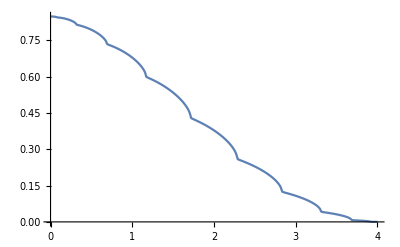

```mathematica
ListLinePlot[Table[{ω,-Im[sl[ω,1][[1,1]]]},{ω,Range[0,4,0.01]}]]
```

```mathematica
ll[ϵ1_,ω_]:=Module[{Tin=T[1],T=T[1],μ1=RandomInteger[{1,10}], μ2=RandomInteger[{1,10}], μ3=RandomInteger[{1,10}], μ4=RandomInteger[{1,10}],μ5=RandomInteger[{1,10}], μ6=RandomInteger[{1,10}], μ7=RandomInteger[{1,10}],μ8=RandomInteger[{1,10}], μ9=RandomInteger[{1,10}], μ10=RandomInteger[{1,10}], μ11=RandomInteger[{1,10}],μ12=RandomInteger[{1,10}], μ13=RandomInteger[{1,10}], μ14=RandomInteger[{1,10}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
lista={{imp3,imp5,imp9,imp11,imp14,imp4,imp6,imp14,imp10,imp3,imp,imp10,imp12,imp14,imp,imp,imp4,imp1,imp9,imp,imp13,imp14,imp4,imp,imp,imp3,imp5,imp,imp,imp14,imp11,imp,imp3,imp7,imp1,imp14,imp11,imp14,imp10,imp3,imp7,imp,imp,imp,imp7,imp7,imp,imp3,imp5,imp12,imp7,imp,imp4,imp,imp6,imp10,imp10,imp2,imp4,imp13,imp12,imp6,imp9,imp6,imp3,imp14,imp11,imp4,imp14,imp2,imp2,imp12,imp,imp9,imp,imp11,imp4,imp2,imp6,imp,imp10,imp1,imp13,imp,imp6,imp,imp,imp6,imp1,imp,imp,imp,imp6,imp12,imp5,imp,imp6,imp7,imp,imp}};
tra:=Module[{},
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[10]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[10]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[10]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
tra]
```

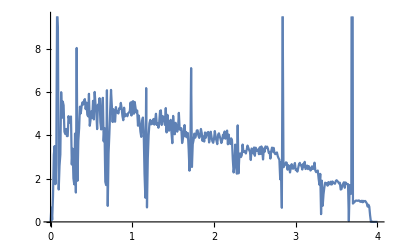

```mathematica
ListLinePlot[Table[{ω,If[ll[0.3,ω]>pris[[ω*100+1,2]],pris[[ω*100+1,2]],ll[0.3,ω]]},{ω,Range[0,4.0,0.01]}]]
```